# Projekt Simulation - Business Mathematics

Thema: Bestimmung der Güte verschiedener Prognose-Modelle für Aktienkursverläufe

Student, Matrikelnummer :
- Antonio Beslic,     5108017
- Büsra Karaoglan, 5056046

In dem folgenden Notebook sind alle Module, welche im Bericht vorkommen und in Mathematica programmiert wurden, enthalten. Als Überschrift über den jeweiligen Code ist das entsprechende Kapitel bzw. Abschnitt angegeben, welcher den Code beinhaltet.

Anmerkungen: 
- die meißten Codes enthalten den Befehl SeedRandom[x]; welcher ein zufälliges Ergebnis festhält. Indem man den Befehl löscht, kriegt man nach jeder Ausführung des Befehls neue Ergebnisse und damit auch eine neue Simulation.

- um die Module aus dem Abschnitt “2.6 Künstliche neuronale Netze in Mathematica” ausführen zu können, braucht man die aktuelle Mathematica Version.

- Beim Einlesen der Daten muss der Pfad für den jeweiligen Rechner angepasst werden.

## Anhang A - Einlesen der Daten in Mathematica

Im Folgenden ist der Code, welcher die Schlusskurse ausliest und nach unserem Belangen richtig formatiert, zu sehen. Die wir lediglich mit den Tagesschlusskursen arbeiten, haben wir das Einlesen der anderen Intraday-Kurse auskommentiert.

### IBM Daten aus dem Jahr 2017 komplett in Sekunden, Minuten, Stunden und Tagesschlusskursen

```mathematica
(* KursSek17=Flatten[Take[Drop[Import["C:\\Users\\toni\\Desktop\\DATEN IBM\\2017_Komplett\\US1.IBM_170101_171231_Sekunden.csv"],1],All,-1]];
KursMin17=Flatten[Take[Drop[Import["C:\\Users\\toni\\Desktop\\DATEN IBM\\2017_Komplett\\US1.IBM_170101_171231_Minuten.csv"],1],All,-1]];
KursStunden17=Flatten[Take[Drop[Import["C:\\Users\\toni\\Desktop\\DATEN IBM\\2017_Komplett\\US1.IBM_170101_171231_Stunden.csv"],1],All,-1]]; *)
KursTage17=Flatten[Take[Drop[Import["C:\\Users\\toni\\Desktop\\DATEN IBM\\2017_Komplett\\US1.IBM_170101_171231_Tage.csv"],1],All,-1]];
```

### IBM Daten aus dem Jahr 2018 Januar-April in Sekunden, Minuten, Stunden und Tagesschlusskursen

```mathematica
(* KursSek18=Flatten[Take[Drop[Import["C:\\Users\\toni\\Desktop\\DATEN IBM\\2018_Januar_April\\US1.IBM_180101_180430_Sekunden.csv"],1],All,-1]];
KursMin18=Flatten[Take[Drop[Import["C:\\Users\\toni\\Desktop\\DATEN IBM\\2018_Januar_April\\US1.IBM_180101_180430_Minuten.csv"],1],All,-1]];
KursStunden18=Flatten[Take[Drop[Import["C:\\Users\\toni\\Desktop\\DATEN IBM\\2018_Januar_April\\US1.IBM_180101_180430_Stunden.csv"],1],All,-1]]; *)
KursTage18=Flatten[Take[Drop[Import["C:\\Users\\toni\\Desktop\\DATEN IBM\\2018_Januar_April\\US1.IBM_180101_180430_Tage.csv"],1],All,-1]];
```

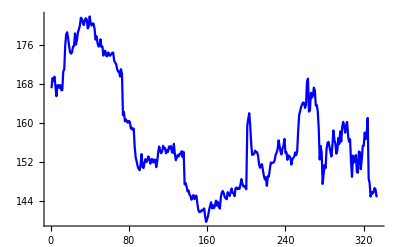

```mathematica
Show[ListLinePlot[Join[KursTage17,KursTage18],PlotStyle->Blue]]
```

## 2.1 M1 : Random Walk ohne Drift

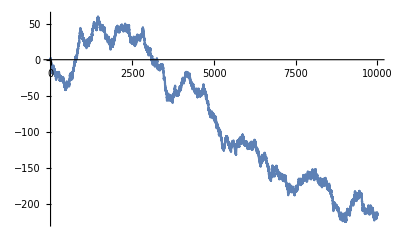

```mathematica
EinfacheIrrfahrtGraphik[Startwert_,n_]:=Module[{y=Startwert,list1=RandomInteger[{0,1},n],list3={}},For[i=1,i≤n,i++,If[list1[[i]]==0,y=y-1,y=y+1];
AppendTo[list3,y]];ListLinePlot[list3]]
SeedRandom[1];EinfacheIrrfahrtGraphik[0,10000]
```

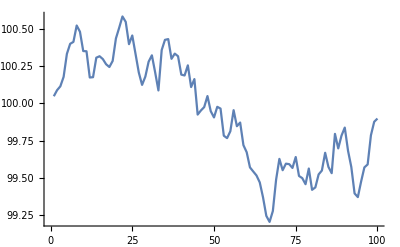

```mathematica
Irrfahrt1[ini_,tmax_]:=Module[{listvalues={}},multipliers=1+RandomVariate[NormalDistribution[],tmax]*0.001;
For[i=1,i≤tmax,i++,values=ini*Product[multipliers[[j]],{j,1,i}];
listvalues=AppendTo[listvalues,values]];
Return[ListLinePlot[listvalues]]]
SeedRandom[1];Irrfahrt1[100,100]
```

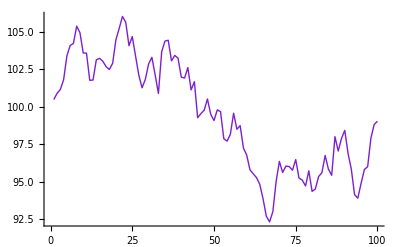

```mathematica
Irrfahrt2[ini_,tmax_,volatility_]:=Module[{listvalues={},vol=volatility},r=RandomVariate[NormalDistribution[],tmax+1]*vol;
For[i=1,i≤tmax,i++,values=ini*Exp[Sum[r[[j]],{j,1,i}]];
listvalues=AppendTo[listvalues,values]];
Return[ListLinePlot[listvalues,PlotStyle->{RandomColor[],Thick}]]]
SeedRandom[1];Irrfahrt2[100,100,0.01]
```

#### Ansatz 1 : Einmalig Parameter mü und sigma schätzen für Prognose, Modul : Modell1[] Für Tagesschlusskurse :

```mathematica
logTage17=Table[Log[KursTage17[[j]]/KursTage17[[j-1]]],{j,2,Length[KursTage17]}];müTage17=Mean[logTage17]; sigmaTage17=StandardDeviation[logTage17];
logTage18=Table[Log[KursTage18[[j]]/KursTage18[[j-1]]],{j,2,Length[KursTage18]}];müTage18=Mean[logTage18]; sigmaTage18=StandardDeviation[logTage18];
```

```mathematica
Modell1[ini_,tmax_,volatility_,müT_]:=Module[{vol=volatility,mü=müT},r=RandomVariate[NormalDistribution[mü,vol],tmax+1];
Table[ini*Exp[Sum[r[[j]],{j,1,i}]],{i,1,tmax}]]
```

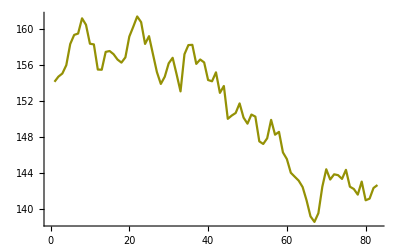

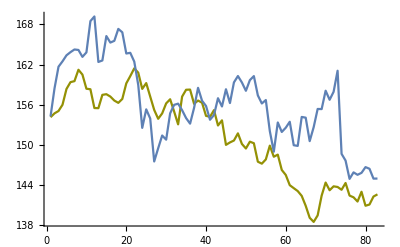

```mathematica
SeedRandom[1];plotModell1=ListLinePlot[Modell1[Last[KursTage17],Length[KursTage18],sigmaTage17,müTage17],PlotStyle->RandomColor[]]
SeedRandom[1];Show[plotModell1,ListLinePlot[KursTage18],PlotRange->All]
```

#### Vergleich der Verteilung der Renditen

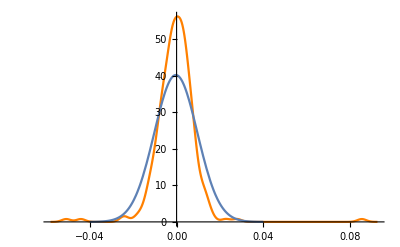

| P-Value
Anderson-Darling | 2.61257×10^-8
Baringhaus-Henze | 7.85074×10^-7
Cramér-von Mises | 0.
Jarque-Bera ALM | 0.
Kolmogorov-Smirnov | 0.
Kuiper | 8.8952×10^-9
Mardia Combined | 0.
Mardia Kurtosis | 1.05555571699194×10^-1382
Mardia Skewness | 1.1955×10^-28
Pearson χ^2 | 5.17539×10^-44
Shapiro-Wilk | 9.5561×10^-18
Watson U^2 | 0.

Reject

```mathematica
Show[SmoothHistogram[logTage17,PlotRange->All,PlotStyle->Orange],Plot[PDF[NormalDistribution[müTage17,sigmaTage17],x],{x,-0.04,0.04}]]
DistributionFitTest[logTage17,Automatic,"HypothesisTestData"]["PValueTable",All]
DistributionFitTest[logTage17,NormalDistribution[müTage17,sigmaTage17],"ShortTestConclusion"]
```

## 2.2 M2 : Random Walk mit angepasster Verteilungsannahme

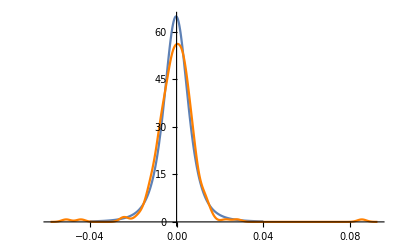

| P-Value
Anderson-Darling | 0.936139
Cramér-von Mises | 0.943745
Kolmogorov-Smirnov | 0.921394
Kuiper | 0.876235
Pearson χ^2 | 0.962986
Watson U^2 | 0.865916

```mathematica
H=DistributionFitTest[logTage17,StudentTDistribution[mu1,sig1,nu1],"HypothesisTestData"];H["FittedDistributionParameters"];Fit1=H["FittedDistribution"];
Show[Plot[PDF[Fit1,x],{x,-0.04,0.04},PlotRange->All],SmoothHistogram[logTage17,PlotStyle->Orange,PlotRange->All]]
DistributionFitTest[logTage17,Fit1,"HypothesisTestData"]["PValueTable",All]
```

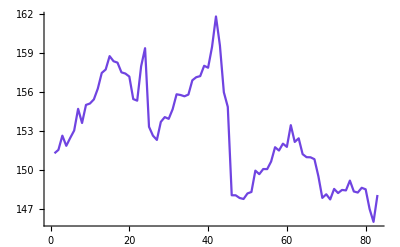

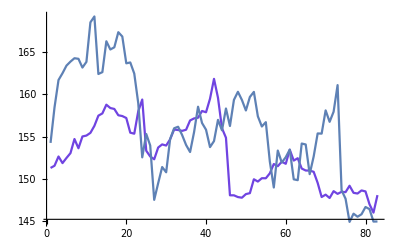

```mathematica
Modell2[ini_,tmax_,volatility_,müT_]:=Module[{vol=volatility,mü=müT},r=RandomVariate[Fit1,tmax+1];
Table[ini*Exp[Sum[r[[j]],{j,1,i}]],{i,1,tmax}]]
SeedRandom[4];plotModell2=ListLinePlot[Modell2[Last[KursTage17],Length[KursTage18],sigmaTage17,müTage17],PlotStyle->RandomColor[]]
SeedRandom[4];Show[plotModell2,ListLinePlot[KursTage18],PlotRange->All]
```

## 2.3 M3 : Geometrische brownsche Bewegung

```mathematica
Modell3[ini_,tmax_,volatility_,müT_]:=Module[{vol=volatility,mü=müT},Table[ini*Exp[(mü-vol^2/2)*i+vol*RandomVariate[NormalDistribution[]]*Sqrt[i]],{i,1,tmax}]]
```

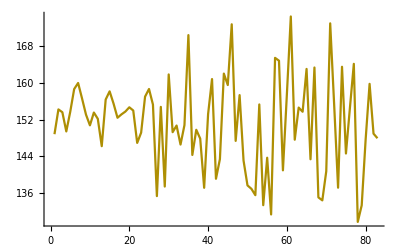

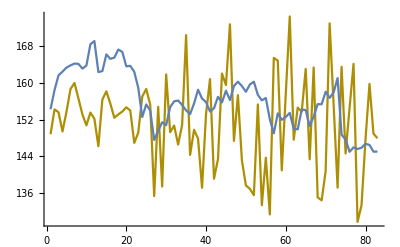

```mathematica
SeedRandom[8];plotModell3=ListLinePlot[Modell3[Last[KursTage17],Length[KursTage18],sigmaTage17,müTage17],PlotStyle->RandomColor[]]
SeedRandom[8];Show[plotModell3,ListLinePlot[KursTage18],PlotRange->All]
```

Im Folgenden sieht man 1000 zufällig simulierte Pfade mit dem Ansatz 3

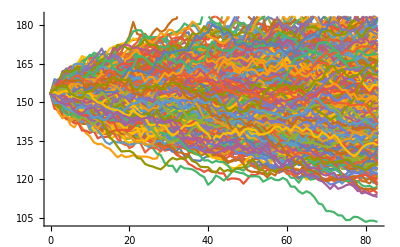

```mathematica
ListLinePlot[Table[RandomFunction[GeometricBrownianMotionProcess[müTage17,sigmaTage17,Last[KursTage17]],{0,Length[KursTage18],1}]["Path"],{1000}]]
```

```mathematica
Mod3=ListLinePlot[Mean[Table[Modell3[Last[KursTage17],50,sigmaTage17,müTage17],100000]],PlotStyle->Black];
Mittelwertsfunktion=ListLinePlot[Table[Exp[t*müTage17]*Last[KursTage17],{t,0,50}],PlotStyle->Green];
```

```mathematica
GeoBroMot=ListLinePlot[Mean[Table[RandomFunction[GeometricBrownianMotionProcess[müTage17,sigmaTage17,Last[KursTage17]],{0,50,1}]["Path"],{100000}]],PlotStyle->Red];
```

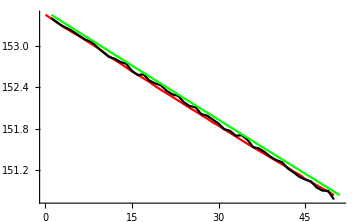

```mathematica
Show[GeoBroMot,Mod3,Mittelwertsfunktion,PlotRange->All]
```

```mathematica
Mean[GeometricBrownianMotionProcess[μ,σ,Subscript[x,0]][t]]//Simplify
```

ⅇ^(t μ) x_0

## 2.4 M4: ARIMA Modell

```mathematica
TimeSeriesModelFit[KursTage17,Automatic]
```

TimeSeriesModel[…]

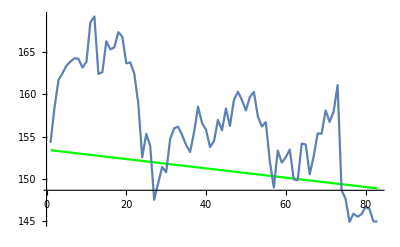

```mathematica
ARIMA[EchtDaten_,tmax_]:=Module[{},TimeSeriesForecast[TimeSeriesModelFit[EchtDaten],{Length[KursTage18]}]["Path"][[All,2]]];
Show[ListLinePlot[ARIMA[KursTage17,Length[KursTage18]],PlotStyle->Green],ListLinePlot[KursTage18],PlotRange->All]
```

## 2.6 Künstliche neuronale Netze in Mathematica

```mathematica
MyNetPrediction[Data_,LengthIn_]:=Module[{DataTraining,Net,NetTrained,DataNetVerify},
DataTraining=RandomSample[Map[List/@Drop[#,-1]->Take[#,{-1}]&,
Partition[Take[Data,{LengthIn,-1}],LengthIn+1,1]]];Net=NetChain[{GatedRecurrentLayer[10],LinearLayer[1]},
"Input"->{LengthIn,1},"Output"->1];
NetTrained=NetTrain[Net,DataTraining];
DataNetVerify=Flatten@NestList[Append[Drop[#,1],NetTrained[#]]&,
List/@Take[Data,{1,LengthIn}],Length[Data]-LengthIn][[All,-1]];
ListLinePlot[{DataNetVerify,Take[Data,{LengthIn,Length[Data]-LengthIn}]},PlotLegends->{"Vorhersage","Sin[x]"}]
];
```

Je nachdem, wann man das Training stoppt, erhält man eine andere Prognose

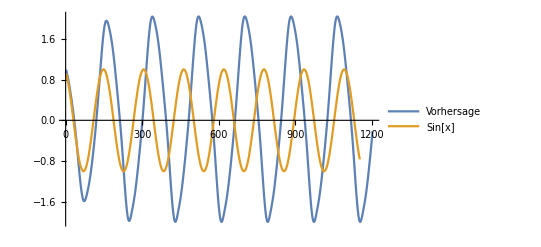

```mathematica
MyNetPrediction[Table[Sin[x],{x,0,50,0.04}],50]
```

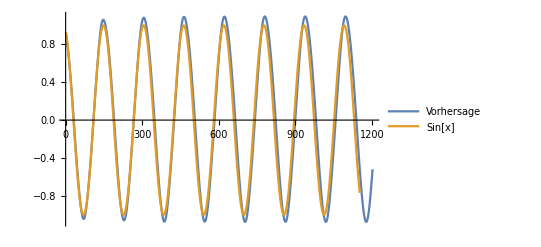

```mathematica
MyNetPrediction[Table[Sin[x],{x,0,50,0.04}],50]
```

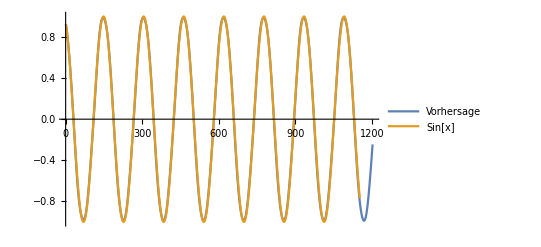

```mathematica
MyNetPrediction[Table[Sin[x],{x,0,50,0.04}],50]
```

Und mit den Aktienkursen :

```mathematica
MyNetPrediction2[Data_,LengthIn_]:=Module[{DataTraining,Net,NetTrained,DataNetVerify},
DataTraining=RandomSample[Map[List/@Drop[#,-1]->Take[#,{-1}]&,
Partition[Take[Data,{LengthIn,-1}],LengthIn+1,1]]];Net=NetChain[{LinearLayer[200],LinearLayer[1]},
"Input"->{LengthIn,1},"Output"->1];
NetTrained=NetTrain[Net,DataTraining];
DataNetVerify=Flatten@NestList[Append[Drop[#,1],NetTrained[#]]&,
List/@Take[Data,{1,LengthIn}],Length[Data]-LengthIn][[All,-1]];
Return[Take[DataNetVerify,LengthIn]]
];
```

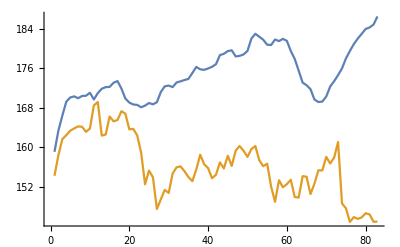

```mathematica
ListLinePlot[{MyNetPrediction2[KursTage17,Length@KursTage18],KursTage18}]
```

## 3 Gütemaße zur Bewertung der Modelle

```mathematica
MAPE[EchtDaten_,Prognose_]:=Module[{A=EchtDaten, F=Prognose,n=Length[EchtDaten]},Total[Abs[(A-F)/A]]/n]
MDA[EchtDaten_,Prognose_]:=Module[{A=EchtDaten, F=Prognose,n=Length[EchtDaten]},1/n*Count[Sign[Differences[A]]-Sign[Differences[F]],0]//N]
MAE[EchtDaten_,Prognose_]:=Module[{A=EchtDaten, F=Prognose,n=Length[EchtDaten]},Total[Abs[(A-F)]]/n]
MAAPE[EchtDaten_,Prognose_]:=Module[{A=EchtDaten, F=Prognose,n=Length[EchtDaten]},Total[ArcTan[Abs[(A-F)/A]]]/n]
MASE[EchtDaten_,Prognose_]:=Module[{A=EchtDaten, F=Prognose,n=Length[EchtDaten]},Total[Abs[A-F]]/((n/(n-1))*Total[Abs[Differences[A]]])]
```

## 4.1 Vergleich und Bewertung der Modelle M1 bis M4

Bemerkung : Die Auswertung für progM1 bis progM4 kann etwas Zeit in Anspruch nehmen.

```mathematica
progM1=Mean[Table[Modell1[Last[KursTage17],Length[KursTage18],sigmaTage17,müTage17],100000]];
progM2=Mean[Table[Modell2[Last[KursTage17],Length[KursTage18],sigmaTage17,müTage17],100000]];
progM3=Mean[Table[Modell3[Last[KursTage17],Length[KursTage18],sigmaTage17,müTage17],100000]];
progM4=ARIMA[KursTage17,Length[KursTage18]];
```

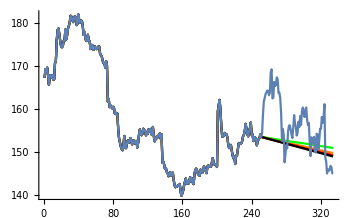

```mathematica
Show[ListLinePlot[Join[KursTage17,progM1],PlotStyle->Orange],ListLinePlot[Join[KursTage17,progM2],PlotStyle->Green],ListLinePlot[Join[KursTage17,progM3],PlotStyle->Red],ListLinePlot[Join[KursTage17,progM4],PlotStyle->Black],ListLinePlot[Join[KursTage17,KursTage18]],PlotRange->All]
```

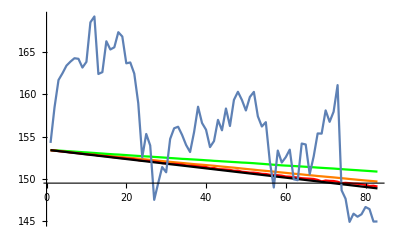

```mathematica
Show[ListLinePlot[progM1,PlotStyle->Orange],ListLinePlot[progM2,PlotStyle->Green],ListLinePlot[progM3,PlotStyle->Red],ListLinePlot[progM4,PlotStyle->Black],ListLinePlot[KursTage18],PlotRange->All]
```

```mathematica
GüteStatistik[m1_,m2_,m3_,m4_]:=Module[{},
mape={"MAPE",MAPE[m1,KursTage18],MAPE[m2,KursTage18],MAPE[m3,KursTage18],MAPE[m4,KursTage18]};
mape=Append[mape,{"Modell ", Flatten[Position[mape,Min[Drop[mape,1]]]-1]}];
mda={"MDA",MDA[m1,KursTage18],MDA[m2,KursTage18],MDA[m3,KursTage18],MDA[m4,KursTage18]};
mda=Append[mda,{"Modell ", Flatten[Position[mda,Max[Drop[mda,1]]]-1]}];mae={"MAE",MAE[m1,KursTage18],MAE[m2,KursTage18],MAE[m3,KursTage18],MAE[m4,KursTage18]};
mae=Append[mae,{"Modell ", Flatten[Position[mae,Min[Drop[mae,1]]]-1]}];maape={"MAAPE",MAAPE[m1,KursTage18],MAAPE[m2,KursTage18],MAAPE[m3,KursTage18],MAAPE[m4,KursTage18]};
maape=Append[maape,{"Modell ", Flatten[Position[maape,Min[Drop[maape,1]]]-1]}];
mase={"MASE",MASE[m1,KursTage18],MASE[m2,KursTage18],MASE[m3,KursTage18],MASE[m4,KursTage18]};
mase=Append[mase,{"Modell ", Flatten[Position[mase,Min[Drop[mase,1]]]-1]}];

Güte=MatrixForm@{{" ","Modell 1","Modell 2","Modell 3","Modell 4","Bestes Modell"},mape,mda,mae,maape,mase}
]
```

```mathematica
stat=GüteStatistik[progM1,progM2,progM3,progM4]
```

(  | Modell 1 | Modell 2 | Modell 3 | Modell 4 | Bestes Modell
MAPE | 0.0390266 | 0.0375819 | 0.0398888 | 0.0401813 | {Modell ,{2}}
MDA | 0.46988 | 0.46988 | 0.493976 | 0.46988 | {Modell ,{3}}
MAE | 5.92905 | 5.72718 | 6.04963 | 6.09017 | {Modell ,{2}}
MAAPE | 0.0389765 | 0.0375357 | 0.039836 | 0.0401275 | {Modell ,{2}}
MASE | 134.057 | 186.499 | 106.524 | 110.892 | {Modell ,{3}})

## 4.2 Bewertung der Prognose von neuronalen Netzen (Ergebnisse aus Python)

```mathematica
Kurs18=Drop[KursTage18,2];
PythonNeuronaleProg=Flatten[Import["C:\\Users\\toni\\Desktop\\PythonPrognose.csv"]];
```

```mathematica
MatrixForm@{{"MAPE",MAPE[PythonNeuronaleProg,Drop[KursTage18,2]]},
{"MDA", MDA[PythonNeuronaleProg,Drop[KursTage18,2]]},
{"MAE", MAE[PythonNeuronaleProg,Drop[KursTage18,2]]},
{"MAAPE", MAAPE[PythonNeuronaleProg,Drop[KursTage18,2]]},
{"MASE", MASE[PythonNeuronaleProg,Drop[KursTage18,2]]}}
```

(MAPE | 0.028629
MDA | 0.45679
MAE | 4.55181
MAAPE | 0.0286064
MASE | 2.02416)